```mathematica
Clear["`*"]
```

## Dimensionless flow equation

```mathematica
dtVbar[rho_]:=-3Vbar[rho]+rho lam1bar[rho]+1/(4 π^2 Ttilde)((Nf^2-1)2/3 1/(√(1+lam1bar[rho]))(1/2+1/(Exp[(√(1+lam1bar[rho]))/Ttilde]-1))+2/3 1/(√(1+(lam1bar[rho]+2rho lam2bar[rho])))(1/2+1/(Exp[(√(1+(lam1bar[rho]+2rho lam2bar[rho])))/Ttilde]-1))-4Nc Nf 2/3 1/(2 √(1+(h^2 rho)/2 Ttilde))(1-1/(Exp[(√(1+(h^2 rho)/2 Ttilde)-mutilde)/Ttilde]+1)-1/(Exp[(√(1+(h^2 rho)/2 Ttilde)+mutilde)/Ttilde]+1)));
dtlam1[rho_]:=D[dtVbar[rho],rho]
dtlam2[rho_]:=D[dtlam1[rho],rho]
dtlam3[rho_]:=D[dtlam2[rho],rho]
rep={lam1bar[rho]->lam1bar,lam2bar[rho]->lam2bar,lam1bar'[rho]->lam2bar,lam2bar'[rho]->lam3bar,Vbar'[rho]->lam1bar,lam1bar''[rho]->lam3bar,lam2bar''[rho]->0,Vbar''[rho]->lam2bar,Derivative[3][lam1bar][rho]->0,Derivative[3][lam2bar][rho]->0,Derivative[3][Vbar][rho]->lam3bar};
dtlam1exp=dtlam1[rho]/.rep/.{rho->0,Nc->3,Nf->2};
dtlam2exp=dtlam2[rho]/.rep/.{rho->0,Nc->3,Nf->2};
dtlam3exp=dtlam3[rho]/.rep/.{rho->0,Nc->3,Nf->2};
dtlam1fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]:=-2 lam1bar+1/(4 π^2 Ttilde)(-8 ((ⅇ^((1-mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(ⅇ^((1+mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1+mutilde)/Ttilde))^2))-(2 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam2bar)/(1+lam1bar)^(3/2)-(2 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar) Ttilde)+2 (1-1/(1+ⅇ^((1-mutilde)/Ttilde))-1/(1+ⅇ^((1+mutilde)/Ttilde))) h^2 Ttilde)
dtlam2fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]:=-lam2bar+1/(4 π^2 Ttilde)((6 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam2bar^2)/(1+lam1bar)^(5/2)-(8 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam3bar)/(3 (1+lam1bar)^(3/2))+(4 ⅇ^((2 √(1+lam1bar))/Ttilde) lam2bar^2)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^3 (1+lam1bar)^(3/2) Ttilde^2)-(2 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^2)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^(3/2) Ttilde^2)+(6 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^2)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^2 Ttilde)-(8 ⅇ^((√(1+lam1bar))/Ttilde) lam3bar)/(3 (-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar) Ttilde)+4 h^2 ((ⅇ^((1-mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(ⅇ^((1+mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1+mutilde)/Ttilde))^2)) Ttilde-3/2 (1-1/(1+ⅇ^((1-mutilde)/Ttilde))-1/(1+ⅇ^((1+mutilde)/Ttilde))) h^4 Ttilde^2-8 (-(ⅇ^((2 (1-mutilde))/Ttilde) h^4)/(8 (1+ⅇ^((1-mutilde)/Ttilde))^3)+(ⅇ^((1-mutilde)/Ttilde) h^4)/(16 (1+ⅇ^((1-mutilde)/Ttilde))^2)-(ⅇ^((2 (1+mutilde))/Ttilde) h^4)/(8 (1+ⅇ^((1+mutilde)/Ttilde))^3)+(ⅇ^((1+mutilde)/Ttilde) h^4)/(16 (1+ⅇ^((1+mutilde)/Ttilde))^2)-(ⅇ^((1-mutilde)/Ttilde) h^4 Ttilde)/(16 (1+ⅇ^((1-mutilde)/Ttilde))^2)-(ⅇ^((1+mutilde)/Ttilde) h^4 Ttilde)/(16 (1+ⅇ^((1+mutilde)/Ttilde))^2)));
dtlam3fun[h_,Ttilde_,mutilde_,lam1bar_,lam2bar_,lam3bar_]:=1/(4 π^2 Ttilde)(-(75 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam2bar^3)/(2 (1+lam1bar)^(7/2))+(27 (1/2+1/(-1+ⅇ^((√(1+lam1bar))/Ttilde))) lam2bar lam3bar)/(1+lam1bar)^(5/2)-(15 ⅇ^((3 √(1+lam1bar))/Ttilde) lam2bar^3)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^4 (1+lam1bar)^2 Ttilde^3)+(15 ⅇ^((2 √(1+lam1bar))/Ttilde) lam2bar^3)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^3 (1+lam1bar)^2 Ttilde^3)-(5 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^3)/(2 (-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^2 Ttilde^3)-(30 ⅇ^((2 √(1+lam1bar))/Ttilde) lam2bar^3)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^3 (1+lam1bar)^(5/2) Ttilde^2)+(15 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^3)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^(5/2) Ttilde^2)+(18 ⅇ^((2 √(1+lam1bar))/Ttilde) lam2bar lam3bar)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^3 (1+lam1bar)^(3/2) Ttilde^2)-(9 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar lam3bar)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^(3/2) Ttilde^2)-(75 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar^3)/(2 (-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^3 Ttilde)+(27 ⅇ^((√(1+lam1bar))/Ttilde) lam2bar lam3bar)/((-1+ⅇ^((√(1+lam1bar))/Ttilde))^2 (1+lam1bar)^2 Ttilde)-9/2 h^4 ((ⅇ^((1-mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(ⅇ^((1+mutilde)/Ttilde) h^2)/(4 (1+ⅇ^((1+mutilde)/Ttilde))^2)) Ttilde^2+15/8 (1-1/(1+ⅇ^((1-mutilde)/Ttilde))-1/(1+ⅇ^((1+mutilde)/Ttilde))) h^6 Ttilde^3+6 h^2 Ttilde (-(ⅇ^((2 (1-mutilde))/Ttilde) h^4)/(8 (1+ⅇ^((1-mutilde)/Ttilde))^3)+(ⅇ^((1-mutilde)/Ttilde) h^4)/(16 (1+ⅇ^((1-mutilde)/Ttilde))^2)-(ⅇ^((2 (1+mutilde))/Ttilde) h^4)/(8 (1+ⅇ^((1+mutilde)/Ttilde))^3)+(ⅇ^((1+mutilde)/Ttilde) h^4)/(16 (1+ⅇ^((1+mutilde)/Ttilde))^2)-(ⅇ^((1-mutilde)/Ttilde) h^4 Ttilde)/(16 (1+ⅇ^((1-mutilde)/Ttilde))^2)-(ⅇ^((1+mutilde)/Ttilde) h^4 Ttilde)/(16 (1+ⅇ^((1+mutilde)/Ttilde))^2))-8 ((3 ⅇ^((3 (1-mutilde))/Ttilde) h^6)/(32 (1+ⅇ^((1-mutilde)/Ttilde))^4)-(3 ⅇ^((2 (1-mutilde))/Ttilde) h^6)/(32 (1+ⅇ^((1-mutilde)/Ttilde))^3)+(ⅇ^((1-mutilde)/Ttilde) h^6)/(64 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(3 ⅇ^((3 (1+mutilde))/Ttilde) h^6)/(32 (1+ⅇ^((1+mutilde)/Ttilde))^4)-(3 ⅇ^((2 (1+mutilde))/Ttilde) h^6)/(32 (1+ⅇ^((1+mutilde)/Ttilde))^3)+(ⅇ^((1+mutilde)/Ttilde) h^6)/(64 (1+ⅇ^((1+mutilde)/Ttilde))^2)+(3 ⅇ^((2 (1-mutilde))/Ttilde) h^6 Ttilde)/(32 (1+ⅇ^((1-mutilde)/Ttilde))^3)-(3 ⅇ^((1-mutilde)/Ttilde) h^6 Ttilde)/(64 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(3 ⅇ^((2 (1+mutilde))/Ttilde) h^6 Ttilde)/(32 (1+ⅇ^((1+mutilde)/Ttilde))^3)-(3 ⅇ^((1+mutilde)/Ttilde) h^6 Ttilde)/(64 (1+ⅇ^((1+mutilde)/Ttilde))^2)+(3 ⅇ^((1-mutilde)/Ttilde) h^6 Ttilde^2)/(64 (1+ⅇ^((1-mutilde)/Ttilde))^2)+(3 ⅇ^((1+mutilde)/Ttilde) h^6 Ttilde^2)/(64 (1+ⅇ^((1+mutilde)/Ttilde))^2)));
```

```mathematica
matrix={D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam1bar],D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam2bar],D[{dtlam1fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam2fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar],dtlam3fun[h,Ttilde,mutilde,lam1bar,lam2bar,lam3bar]},lam3bar]};
```

```mathematica
Clear[fixedPoints]
```

```mathematica
fixedPoints[t_?NumericQ,mu_?NumericQ,a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=fixedPoints[t,mu]=FindRoot[{dtlam1fun[13/2,t,mu,lam1bar,lam2bar,lam3bar]==0,dtlam2fun[13/2,t,mu,lam1bar,lam2bar,lam3bar]==0,dtlam3fun[13/2,t,mu,lam1bar,lam2bar,lam3bar]==0},{{lam1bar,a1},{lam2bar,a2},{lam3bar,a3}},AccuracyGoal->15,PrecisionGoal->15,Method->{"Newton", "StepControl" -> "TrustRegion"}];
```

```mathematica
fixedPoints[20,0,-0.21951219512195122,2.639493743864411,14.87729250936843]
```

{lam1bar→-0.219504,lam2bar→2.63958,lam3bar→14.8781}

```mathematica
fixedPoints[100,0]
```

fixedPoints[100,0]

```mathematica
Table[fixedPoints[t,0,lam1bar,lam2bar,lam3bar]/.fixedPoints[t+1/10,0],{t,20-1/10,1,-1/10}];
```

```mathematica
Table[fixedPoints[t,0,lam1bar,lam2bar,lam3bar]/.fixedPoints[t+1/100,0],{t,1-1/100,1/100,-1/100}];
```

```mathematica
Table[fixedPoints[t,1/2,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,0],{t,20,1,-1/10}];
```

```mathematica
Table[fixedPoints[t,1/2,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,0],{t,1-1/100,1/100,-1/100}];
```

```mathematica
Table[fixedPoints[t,2/3,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,1/2],{t,20,1,-1/10}];
```

```mathematica
Table[fixedPoints[t,2/3,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,1/2],{t,1-1/100,1/100,-1/100}];
```

```mathematica
Table[fixedPoints[t,3/4,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,2/3],{t,20,1,-1/10}];
```

```mathematica
Table[fixedPoints[t,3/4,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,2/3],{t,1-1/100,1/100,-1/100}];
```

```mathematica
Table[fixedPoints[t,4/5,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,3/4],{t,20,1,-1/10}];
```

```mathematica
Table[fixedPoints[t,4/5,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,3/4],{t,1-1/100,1/100,-1/100}];
```

General::munfl: 1/((1.48938×10^78)^4) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

```mathematica
Table[fixedPoints[t,33/40,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,4/5],{t,20,1,-1/10}];
Table[fixedPoints[t,33/40,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,4/5],{t,1-1/100,1/100,-1/100}];
```

General::munfl: 1/((1.81444×10^79)^4) 太小，不适合被表示为归一化机器数；可能无法保持原来的精度.

```mathematica
Table[fixedPoints[t,37/40,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,33/40],{t,20,1,-1/10}]//Quiet;
Table[fixedPoints[t,37/40,lam1bar,lam2bar,lam3bar]/.fixedPoints[t,33/40],{t,1-1/100,1/100,-1/100}]//Quiet;
```

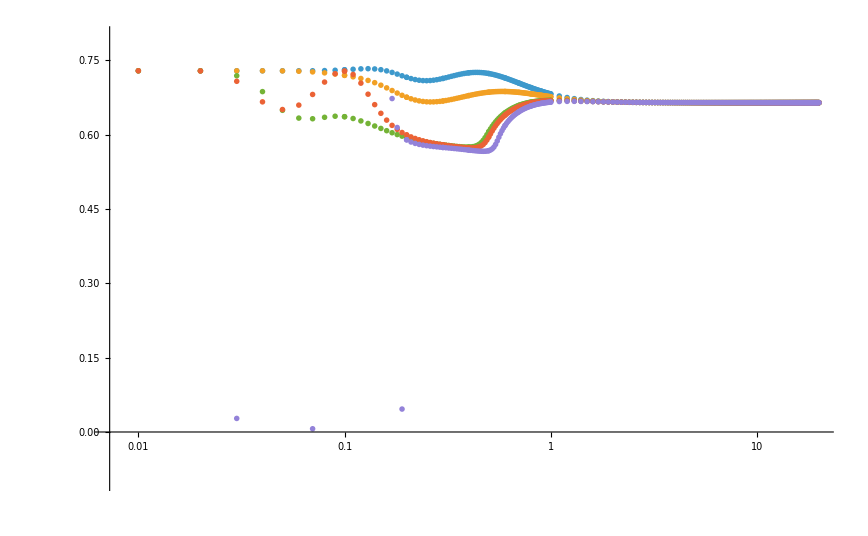

```mathematica
ListPlot[{Flatten[{Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->0,h->13/2}/.fixedPoints[t,0]]][[1]]},{t,20,1/10,-1/10}],Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->0,h->13/2}/.fixedPoints[t,0]]][[1]]},{t,1,1/100,-1/100}]},1],Flatten[{Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->1/2,h->13/2}/.fixedPoints[t,1/2]]][[1]]},{t,20,1/10,-1/10}],Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->1/2,h->13/2}/.fixedPoints[t,1/2]]][[1]]},{t,1,1/100,-1/100}]},1],Flatten[{Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->4/5,h->13/2}/.fixedPoints[t,4/5]]][[1]]},{t,20,1/10,-1/10}],Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->4/5,h->13/2}/.fixedPoints[t,4/5]]][[1]]},{t,1,1/100,-1/100}]},1],Flatten[{Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->33/40,h->13/2}/.fixedPoints[t,33/40]]][[1]]},{t,20,1/10,-1/10}],Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->33/40,h->13/2}/.fixedPoints[t,33/40]]][[1]]},{t,1,1/100,-1/100}]},1],Flatten[{Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->37/40,h->13/2}/.fixedPoints[t,37/40]]][[1]]},{t,20,1/10,-1/10}],Table[{t,-1/Sort[Eigenvalues[matrix/.{Ttilde->t,mutilde->37/40,h->13/2}/.fixedPoints[t,37/40]]][[1]]},{t,1,1/100,-1/100}]},1]},PlotRange->{All,{-0.1,0.8}},ScalingFunctions->{"Log",Automatic}]
```

```mathematica
150/0.01
```

15000.

```mathematica
fixp1=Table[fixedPoints[t,0,lam1bar,lam2bar,lam3bar]/.fixedPoints[t+1/10,0],{t,20-1/10,1,-1/10}];
```

```mathematica
fixp2=Table[fixedPoints[t,0,lam1bar,lam2bar,lam3bar]/.fixedPoints[t+1/100,0],{t,1-1/100,1/100,-1/100}];
```

```mathematica
lam2bar1=Table[fixp1[[i]][[2]][[2]],{i,1,Length[fixp1]}];
lam2bar2=Table[fixp2[[i]][[2]][[2]],{i,1,Length[fixp2]}];
```

```mathematica
Length[fixp2]
```

99

```mathematica
lam21=Table[{20-1/10-i*1/10,lam2bar1[[i]]/(20-1/10-i*1/10)},{i,1,190,1}];
lam22=Table[{1-1/100-i*1/100,lam2bar1[[i]]/(1-1/100-i*1/100)},{i,1,98,1}];
```

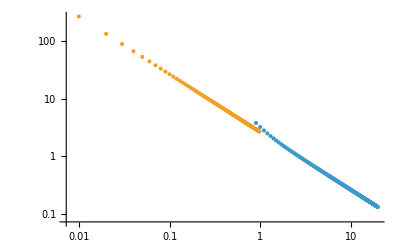

```mathematica
ListPlot[{lam21,lam22},ScalingFunctions->{"Log","Log"}]
```